```mathematica
ClearAll
Clear[d,nu,L,c,g,mu,NU,LL]
d[nu_,L_,c_,mu_] = -(1+nu^2)^2 + c nu + mu - L;
d1[nu_,L_,c_,mu_] = D[d[nu,L,c,mu],nu];
clin[mu_] = 4*(2+Sqrt[1+6*mu])Sqrt[-1 + Sqrt[1+6mu]]/(3Sqrt[3]);
mu0 = 1/4;c0=clin[mu0];
nul[L_]  =nu/.Solve[d[nu,L,c0,mu0]==0,nu];
SOL[g_] = {nu,L}/.Solve[{d[nu,L,c0,mu0]==0,d[nu+I g,L,c0,mu0]==0},{nu,L}];
LAM[g_,jj_] := SOL[g][[jj,2]];
NU[g_,jj_] := SOL[g][[jj,1]];
ess[g_] =L/. Solve[d[I g,L,c0,mu0]==0,L];
essn[g_,eta_] =L/. Solve[d[I g-eta,L,c0,mu0]==0,L];
```

ClearAll

```mathematica
(* Check that LAM[g,jj] gives actual absolute spectrum*)
NSolve[d[nu,LAM[0.5,2],c0,mu0]==0,nu]
```

{{nu→-0.518289-1.68756 ⅈ},{nu→-0.228981+0.796325 ⅈ},{nu→-0.228981+1.29633 ⅈ},{nu→0.976251-0.405089 ⅈ}}

```mathematica
NU[g][[1]]
```

{-(-9+√273)^(1/3)/(2 3^(2/3))+2/(3 (-9+√273))^(1/3)-ⅈ g,1/72 (-6-(96 3^(1/3))/(-9+√273)^(2/3)+(36 3^(2/3))/(-9+√273)^(1/3)-9 (3 (-9+√273))^(1/3)-2 (3 (-9+√273))^(2/3)-144 g^2+(576 3^(1/3) g^2)/(-9+√273)^(2/3)+12 (3 (-9+√273))^(2/3) g^2-(192 ⅈ 3^(2/3) g^3)/(-9+√273)^(1/3)+48 ⅈ (3 (-9+√273))^(1/3) g^3-72 g^4)}

```mathematica
ParametricPlot[ReIm[NU[g]],{g,-1.5,1.5}]
```

-Graphics-

-0.304823+1.92721 ⅈ

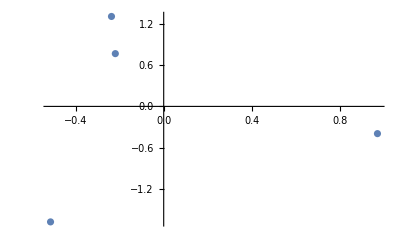

```mathematica
L0 = LAM[0.3,2]
ListPlot[ReIm[nul[L0]]]
```

```mathematica
NU[0.,2]
```

-0.220064+1.07018 ⅈ

```mathematica
N[clin[mu0]]
```

2.10155

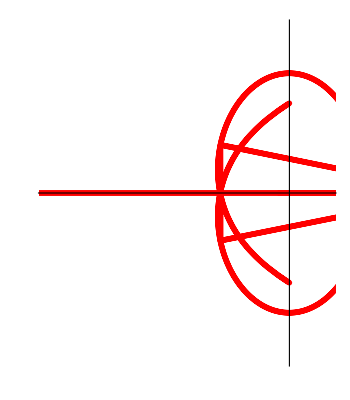

```mathematica
ParametricPlot[{ReIm[LAM[g,1;;3]]},{g,-5,5},WorkingPrecision->20,PlotRange->{{-6,1},{-4,4}},PlotTheme->"Minimal",PlotStyle->{{Thickness[0.01],Red},{Thickness[0.01],Orange},{Thickness[0.01],Green},{Thickness[0.01],Blue},{Thickness[0.01],Blue}},LabelStyle->Directive[Bold]]
```

ParametricPlot::precw: The precision of the argument function ({(-4 ⅈ √(6 (-2+Power[«2»]))-2 ⅈ √(15 (-2+Power[«2»]))+√(-192-156 (-2+Power[«2»])-48 √10 (-2+Power[«2»])+15.4797 g^2-0.416009 g^4+0.00372668 g^6))-0,(-192-156 (-2+√10)-«1»+«1»-0.416009 g^4+0.00372668 g^6)-0,«1»,Im[15.4797 g^2-0.416009 g^4+0.00372668 g^6]-0}) is less than WorkingPrecision (20.).

ParametricPlot::precw: The precision of the argument function ({True,True,Re[√(-192-156 (-2+Power[«2»])-48 √10 (-2+Power[«2»])+15.4797 g^2-0.416009 g^4+0.00372668 g^6)]≤0,-192-156 (-2+√10)-48 √10 (-2+√10)+Re[15.4797 g^2-0.416009 g^4+0.00372668 g^6]≤0}) is less than WorkingPrecision (20.).

ParametricPlot::precw: The precision of the argument function ({(-4 ⅈ √(6 (-2+Power[«2»]))-2 ⅈ √(15 (-2+Power[«2»]))+√(-192-156 (-2+Power[«2»])-48 √10 (-2+Power[«2»])+15.4797 g^2-0.416009 g^4+0.00372668 g^6))-0,(-192-156 (-2+√10)-«1»+«1»-0.416009 g^4+0.00372668 g^6)-0,«1»,Im[15.4797 g^2-0.416009 g^4+0.00372668 g^6]-0}) is less than WorkingPrecision (20.).

General::stop: Further output of ParametricPlot::precw will be suppressed during this calculation.

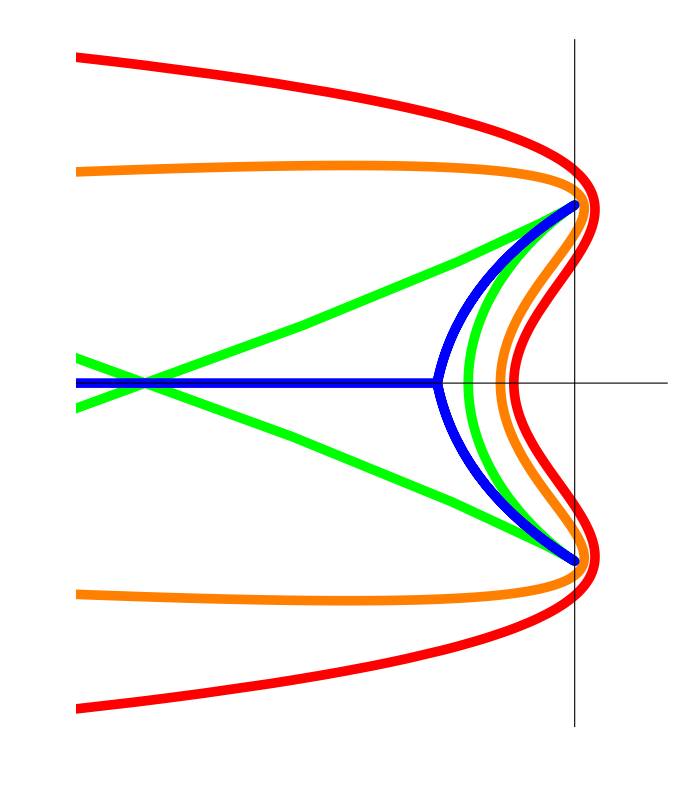

```mathematica
ParametricPlot[{ReIm[ess[g]],ReIm[essn[g,Re[-NU[0.,2]/3]]],ReIm[essn[g,Re[-NU[0.,2]]]],ReIm[LAM[g/3.05,1;;2]],{ReIm[g-1.70-5]}},{g,-5,5},WorkingPrecision->20,PlotRange->{{-6,1},{-4,4}},PlotTheme->"Minimal",PlotStyle->{{Thickness[0.01],Red},{Thickness[0.01],Orange},{Thickness[0.01],Green},{Thickness[0.01],Blue},{Thickness[0.01],Blue}},LabelStyle->Directive[Bold]]
```

```mathematica
ess[1]
```

{1/36 (9+8 ⅈ (2 √(6 (-2+√10))+√(15 (-2+√10))))}

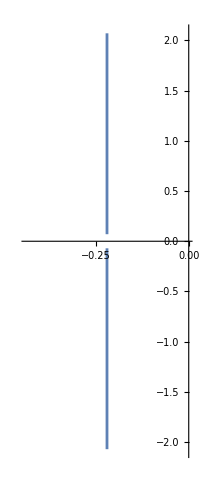

```mathematica
ParametricPlot[{ReIm[NU[g,2;;3]]},{g,-1,1}]
```

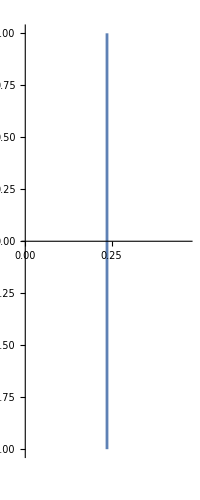

```mathematica
ParametricPlot[{ReIm[NU[g,1]]},{g,-1,1}]
```

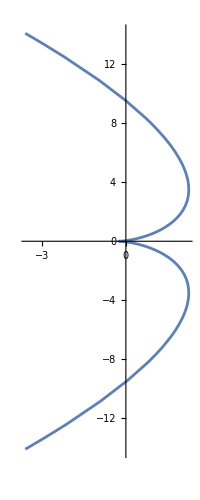

```mathematica
ParametricPlot[{ReIm[LAM[g,1]]},{g,-2,2}]
```